Need to worry about “metastable” states...

```mathematica
diameter={5.0,5.5,6.0,6.5,7.0,7.5,8.0,8.5,9.0,9.5,10.0,10.5,11.0,11.5,12.0,12.5,13.0,13.5,14.0,14.5,15.0,15.5,16.0,16.5,17.0,17.5,18.0,18.5,19.0,19.5,20,21.0,22.0,23.0,24.0,30};
```

```mathematica
volume = (4 π)/3(diameter/2)^3;
```

```mathematica
domainEnergy = {0.13331,0.47125,0.278,0.56,0.8878,0.67669,1.847,1.8687,1.775,1.51,1.99,1.93,4.1,4.71,4.33,6.82,7.75,6.59,9.25,11.12,10.94,10.1,15.74,17.7,10.32};
```

```mathematica
electrostaticEnergy= {0.115,0.1839,0.2216,0.3455,0.33525,0.69943,0.7445,0.7264,0.835,1.19,1.248,1.06,2.66,2.43,2.89,2.51,3.35,3.09,3.44,4.02,5.71,5.08,6.06,7.52,5.39};
```

```mathematica
totalEnergy= {-5.585,-6.175,-7.4179,-9.41,-11.46,-13.5,-22.29,-22.56,-22.202,-28.87,-36.36,-37.25,-37.38,-46.83,-51.3,-57.18,-71.29,-83.18,-88.223,-95.4,-103.56,-116.24,-126.49,-142.6,-159.95};
```

```mathematica
Length[domainEnergy]
```

25

```mathematica
s=ListPlot[Table[{volume[[k]]*10^-3,domainEnergy[[k]]},{k,1,25}],PlotStyle->{Thick,Blue},ImageSize->700,Frame->{True,True,False,False},
FrameTicksStyle->Directive[Black,18],
BaseStyle->Directive[{Black,FontWeight->"Bold",FontSize->14,FontFamily->"Latin Modern Roman",FontColor->Black}],
FrameLabel->{Style["Volume [10^3nm^3]",FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->22],Style["E [arb units]",FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->22]},
PlotLegends->Placed[LineLegend[{Directive[Blue,DotDashed,Thickness[0.0025]],Directive[Red,Thickness[0.0025]]},(*can use linelegend with a frame, use Directive on the {Directive[Black,Dashing..],Black,"0","10"} to get hte proper dashing, then use text annotations with the color for strains*)
{Style["E_wall",FontSize->15],
Style["E_electrostatic ; ΔE ≂  7 * 10^-5",FontSize->15]
}],{{0.418,0.82},{0.8,0.3}}]];t=ListPlot[Table[{volume[[k]]*10^-3,electrostaticEnergy[[k]]},{k,1,25}],PlotStyle->{Thick,Red}];
u= ListPlot[Table[{volume[[k]]*10^-3,totalEnergy[[k]]},{k,1,25}],ImageSize->700,Frame->{True,True,False,False},
FrameTicksStyle->Directive[Black,18],PlotStyle->Green,
BaseStyle->Directive[{Black,FontWeight->"Bold",FontSize->14,FontFamily->"Latin Modern Roman",FontColor->Black}],
FrameLabel->{Style["Volume [10^3nm^3]",FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->22],Style["Total E [arb units]",FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->22]}];
```

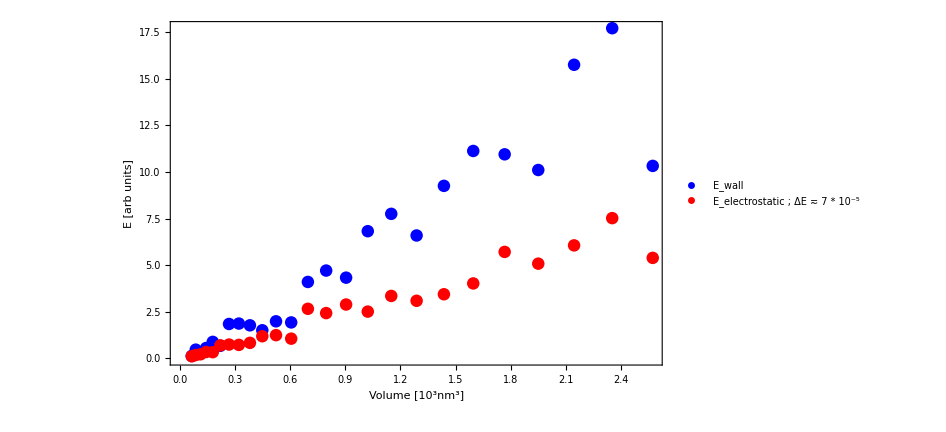

```mathematica
Show[{s,t}]
```

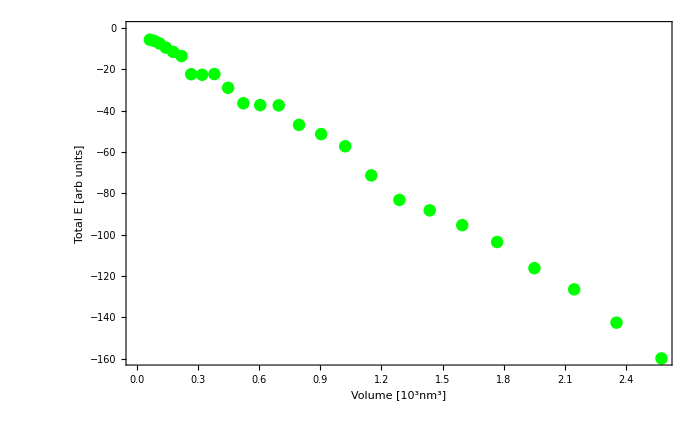

```mathematica
u
```